```mathematica
Kf=579.927;
Kr=559.386;(*Nm/°*)
Ktr=10000;
```

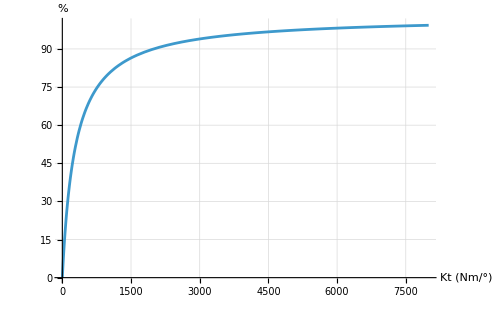

```mathematica
Plot[(1/(1/Kf+1/Kr+1/Kt))/(1/(1/Kf+1/Kr+1/Ktr))*100,{Kt,0,8000},GridLines->Automatic,ImageSize->500,AxesLabel->{"Kt (Nm/°)","%"},PlotRange->{0,100}]
```

Wanted stiffness value

```mathematica
NSolve[(1/(1/Kf+1/Kr+1/Kt))/(1/(1/Kf+1/Kr+1/Ktr))*100==95,Kt]
```

{{Kt→3447.01}}

Stiffness calculated by ansys

```mathematica
L=0.595266;
F=100;
T=2*L*F
```

119.053

```mathematica
δ=(0.38031(*mm*))/1000;
θ=N[ArcSin[δ/L]*180/π]
```

0.0366058

```mathematica
K=T/θ
```

3252.31

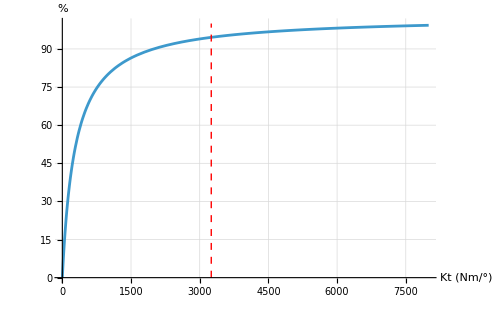

```mathematica
Plot[(1/(1/Kf+1/Kr+1/Kt))/(1/(1/Kf+1/Kr+1/Ktr))*100,{Kt,0,8000},GridLines->Automatic,ImageSize->500,AxesLabel->{"Kt (Nm/°)","%"},Epilog->{Thick,Red,Dashed,Line[{{K,0},{K,100}}]},PlotRange->{0,100}]
```

```mathematica
(1/(1/Kf+1/Kr+1/Kt))/(1/(1/Kf+1/Kr+1/Ktr))*100/.Kt->K
```

94.568

Improvement

```mathematica
100*K/1988
```

163.597